## Suboptimal r(x_0)=u/x_R [δ(x_0-x_R)+δ(x_0+x_R)] for the sixth order polynomial distribution

```mathematica
pbc[a_,xT_]:= a xT^2+(4-3 a) xT^4+7/30 (-9+8 a) xT^6;
```

```mathematica
Manipulate[Plot[pbc[a,x],{x,0,1}],{a,0,1/23 (117+√8169)}]
```

### Solution of the MFPT equation for this family of resetting functions

```mathematica
sol1=DSolve[{F1''[x0]==-1,F2''[x0]==-1,F1[-1]==0,F2[0]==0,F1[-xR]==F2[-xR],F2'[-xR]-F1'[-xR]==u/xR*F1[-xR]},{F1[x0],F2[x0]},x0]
```

{{F1[x0]→(x0+u x0+x0^2+u x0^2+u xR-u x0^2 xR-u xR^2-u x0 xR^2)/(2 (-1-u+u xR)),F2[x0]→(x0+x0^2+u x0^2+u x0 xR-u x0^2 xR-u x0 xR^2)/(2 (-1-u+u xR))}}

```mathematica
FullSimplify[-F2[x0]/.sol1[[1]]/.x0->x]
```

(x (-1+x (-1+u (-1+xR))+u (-1+xR) xR))/(-2+2 u (-1+xR))

```mathematica
sol2=DSolve[{F1''[x0]==-1,F2''[x0]==-1,F3''[x0]==-1,F1[-1]==0,F2[0]==0,F1[-xR]==F2[-xR],F2'[-xR]-F1'[-xR]==u/xR*F1[-xR],F2[xR]==F3[xR],F3'[xR]-F2'[xR]==u/xR*F2[xR]},{F1[x0],F2[x0],F3[x0]},x0]
```

{{F1[x0]→(x0+u x0+x0^2+u x0^2+u xR-u x0^2 xR-u xR^2-u x0 xR^2)/(2 (-1-u+u xR)),F2[x0]→(x0+x0^2+u x0^2+u x0 xR-u x0^2 xR-u x0 xR^2)/(2 (-1-u+u xR)),F3[x0]→(x0+u x0+x0^2+u x0^2-u xR+2 u x0 xR+2 u^2 x0 xR-u x0^2 xR-u xR^2-2 u^2 xR^2-u x0 xR^2-2 u^2 x0 xR^2+2 u^2 xR^3)/(2 (-1-u+u xR))}}

```mathematica
FullSimplify[-F3[x0]/.sol2[[1]]/.x0->x]
```

(-((1+u) x (1+x))+u (1-2 (1+u) x+x^2) xR+u (1+2 u) (1+x) xR^2-2 u^2 xR^3)/(-2+2 u (-1+xR))

```mathematica
Manipulate[Show[Plot[(x (-1+x (-1+u (-1+xR))+u (-1+xR) xR))/(-2+2 u (-1+xR)),{x,0,xR}],Plot[(-((1+u) x (1+x))+u (1-2 (1+u) x+x^2) xR+u (1+2 u) (1+x) xR^2-2 u^2 xR^3)/(-2+2 u (-1+xR)),{x,xR,1}],PlotRange->All],{{xR,0.7},0,1},{{u,11},0,20}]
```

### Average MFPT over the distribution

```mathematica
FullSimplify[Integrate[pbc[a,x]*(x (-1+x (-1+u (-1+xR))+u (-1+xR) xR))/(-2+2 u (-1+xR)),{x,0,xR}]+Integrate[pbc[a,x]*(-((1+u) x (1+x))+u (1-2 (1+u) x+x^2) xR+u (1+2 u) (1+x) xR^2-2 u^2 xR^3)/(-2+2 u (-1+xR)),{x,xR,1}]]
```

1/(30240 (-1+u (-1+xR)))(-11223 (1+u)+9 u xR (50+7 xR (217+xR^4 (1+xR) (-32+9 xR^2))-14 u (97+xR (-217+120 xR+(-1+xR) xR^5 (-32+9 xR^2))))+4 a (143+u (-1+xR) (-143+63 xR (-3+2 u (-1+5 xR^4-6 xR^6+2 xR^8)+xR (-2+xR (-2+xR (3+2 xR (4+xR-xR^2 (2+xR)))))))))

```mathematica
(*Plot of average MFPT for a->9 as a function of xR and u*)
```

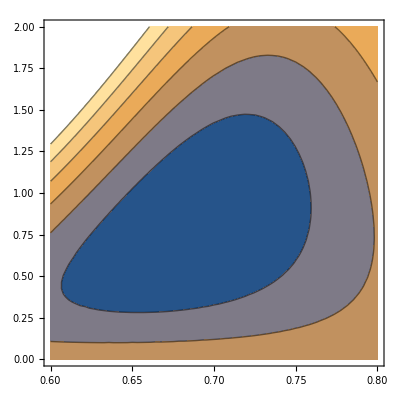

```mathematica
ContourPlot[1/(30240 (-1+u (-1+xR)))(-11223 (1+u)+9 u xR (50+7 xR (217+xR^4 (1+xR) (-32+9 xR^2))-14 u (97+xR (-217+120 xR+(-1+xR) xR^5 (-32+9 xR^2))))+4 a (143+u (-1+xR) (-143+63 xR (-3+2 u (-1+5 xR^4-6 xR^6+2 xR^8)+xR (-2+xR (-2+xR (3+2 xR (4+xR-xR^2 (2+xR)))))))))/.a->9,{xR,0.6,0.8},{u,0,2}]
```

```mathematica
sol[a_]:=FindMinimum[{1/(30240 (-1+u (-1+xR)))(-11223 (1+u)+9 u xR (50+7 xR (217+xR^4 (1+xR) (-32+9 xR^2))-14 u (97+xR (-217+120 xR+(-1+xR) xR^5 (-32+9 xR^2))))+4 a (143+u (-1+xR) (-143+63 xR (-3+2 u (-1+5 xR^4-6 xR^6+2 xR^8)+xR (-2+xR (-2+xR (3+2 xR (4+xR-xR^2 (2+xR))))))))),xR>0,u>0,xR<1},{{xR,0.68},{u,0}}]
```

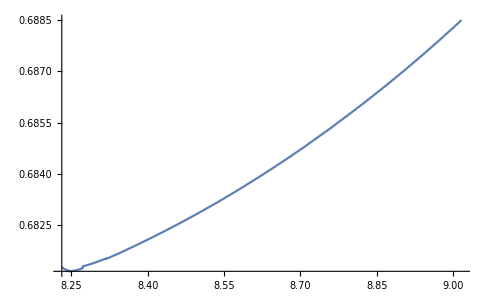

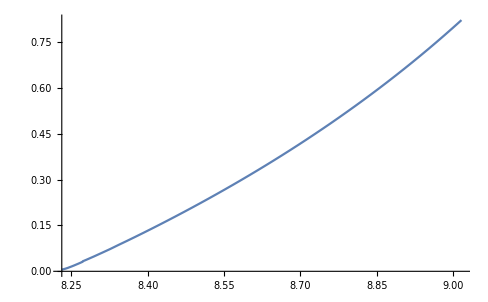

```mathematica
Plot[xR/.sol[a][[2]],{a,8.23125087476942,1/23 (117+√8169)}]
Plot[u/.sol[a][[2]],{a,8.23125087476942,1/23 (117+√8169)}]
```

```mathematica
xR/.sol[8.5][[2]]
xR/.sol[8.75][[2]]
xR/.sol[9][[2]]
u/.sol[8.5][[2]]
u/.sol[8.75][[2]]
u/.sol[9][[2]]
```

0.682857

0.685238

0.688264

0.21964

0.472825

0.796163